# Designing the Brick Wall of the Future

MonthName Day, Year

Chris Carlson, User Interface Group

I created this design for a brick wall in Mathematica. Constructing it would be tedious and technically demanding work indeed, requiring numerous jigs and repeated measurements, not to mention an unusually skilled mason. Or a robot.

-Graphics-

A few groups have begun to experiment with the idea of robotically laid brick construction, most notably the Swiss firm Gramazio & Kohler (Facade Gantenbein Winery, Structural Oscillations), and recently, students at the Harvard University Graduate School of Design (On the Bri(n)ck). Inspired by these efforts, I set out to investigate the possibilities of robotic brick-wall construction with Mathematica.

In many ways, Mathematica is the ideal tool for exploring this domain. If you are moderately fluent in Mathematica, it's straightforward to go from an idea of a wall construction to a Mathematica program that produces it. You can easily, interactively explore parametric variations of your ideas, and you can bring the wealth of functions built into Mathematica to bear on the problem, to explore ideas that are on, or beyond, the fringes of what would be possible with other programs.

There are lots of possible effects to investigate: displacing bricks, rotating them, leaving gaps between them, creating ledges of various depths for shadow effects, combining bricks of various colors, and so on. To warm up to the problem, I began by dashing off code for a brick screen of given dimensions.

```mathematica
Manipulate[
Graphics3D[{0.8506752117189288,EdgeForm[Gray],
Table[With[{
x=(bl+bs) (b + If[EvenQ[c],0,.5]),
y=0,
z=bh c 
},Cuboid[{x,y,z},{x,y,z}+{bl,bw,bh}]],{c,0,Floor[wh/bh]-1},{b,0,Ceiling[wl/bl]-1}]},
Boxed->False,Lighting->"Neutral"
],
{{wl,32,"wall length"},1,100},
{{wh,32, "wall height"},1,100},
Delimiter,
{{bl,8,"brick length"},0,16},
{{bw,4,"brick width"},0,16},
{{bh,2,"brick height"},0,16},
{{bs,1,"brick spacing"},0,16}
]
```

From that starting point, the first effect I explored was varying the gaps between the bricks. Each brick in the wall above has a nominal horizontal position. By displacing the bricks from their nominal positions by an amount governed by a function of the bricks' positions, I was able to generate a variety of interesting architectural screens. I used a combination of horizontal and vertical sinusoids to govern the displacements, and modified my previous code to make this Manipulate, with which I could experiment with the sinusoid frequencies.

```mathematica
Manipulate[
Module[{nc=Floor[wh/bh],nb=Ceiling[wl/(bl+bs)]},
Graphics3D[{0.8506752117189288,EdgeForm[None],
Table[With[{
x=(bl+bs) (b + If[EvenQ[c],0,.5])+bs a Cos[2 π  hf b/nb]Cos[2 π vf  c/nc],
y=0,
z=bh c 
},Cuboid[{x,y,z},{x,y,z}+{bl,bw,bh}]],{c,0,nc-1},{b,0,nb-1}]},
Boxed->False,Lighting->"Neutral"
]],
{{bl,8,"brick length"},0,16},
{{bw,4,"brick width"},0,16},
{{bh,2,"brick height"},0,16},
{{bs,1.5,"brick spacing"},0,16},
Delimiter,
{{wl,100,"wall length"},1,200},
{{wh,61, "wall height"},1,200},
Delimiter,
{{hf,2,"horizontal frequency"},0,8,.5},
{{vf,.5,"vertical frequency"},0,8,.5},
{{a,1,"amplitude"},0,1},
ControlPlacement->Top
]
```

Here are some of the resulting screens (click an image to enlarge it).

-Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D-

As I was thinking about the effects that could be achieved by slightly displacing bricks, it occurred to me that stereograms work similarly: by varying the displacements of corresponding points in left and right images, a stereogram gives the illusion of three dimensions. With the precision placement of bricks made possible by a robot, it ought to be possible to build a flat wall that would undulate in 3D when viewed as a stereogram. I prototyped the idea in a 2D view of such a wall with this code.

```mathematica
With[{bl=8,bw=4,bh=2,wl=240,wh=120,bs=2},
Module[{nc=Floor[wh/bh],nb=Ceiling[wl/(bl+bs)]},
Framed[Graphics[{0.4977340352483406,EdgeForm[White],
Table[Module[{
x=(bl+bs) (b + If[EvenQ[c],0,.5])+bs,
y=bh c, xn, yn,r=.2
},
x += 1.5 Sin[π (2 b/(nb-1)-.5) ]Cos[π(2 c/(nc-1)-1) ];
With[{brick=Rectangle[{x,y},{x,y}+{bl,bh}]},
If[c==wh/bh/2&&(b==(wl/(bl+bs))/4||b==(3 wl/(bl+bs))/4),{Black,brick},brick]]
],{c,0,nc-1},{b,0,nb-1}]
},ImageSize->{400,200}
]//HiRes]]
]
```

-Graphics-

When you view the wall cross-eyed so that the black bricks fuse at the center, you'll see the 3D surface that I plotted below. The effect is subtle, and it requires some patience and skill at free-viewing stereograms, but it's unmistakable when you attain it. If you view the image "wall-eyed", the 3D surface will be inverted.

```mathematica
Plot3D[Sin[π  xn]Cos[2 π  yn],{xn,-.5,.5},{yn,-.5,.5},ViewPoint->{0,.8,3.3},ViewVertical->{0,0,1},Axes->None,Boxed->False,ImageSize->200]
```

-Graphics3D-

After the stereogram, I explored displacing bricks perpendicularly to the wall to produce wavy wall surfaces. For this experiment I took a different tack, after I realized the analogy of what I wanted to do to Mathematica's Plot3D function. Plot3D plots a surface with height given by a function of {x, y} position, as shown here:

```mathematica
Plot3D[Sin[(7 (x/128-.5))^2+(7 (y/128-.25))^2],{x,0,128},{y,0,64},BoxRatios->Automatic]
```

-Graphics3D-

I wanted to construct a brick wall with bricks displaced from the plane of the wall by an amount given by a function of the bricks' positions. So I wrote a drop-in replacement for Plot3D called BrickPlot that plots a surface using bricks.

```mathematica
BrickPlot[Sin[(7 (x/128-.5))^2+(7 (y/128-.25))^2],{x,0,128},{y,0,64},StandardWallView[]]
```

-Graphics3D-

BrickPlot demonstrates why Mathematica is particularly well suited to this exploration. In order to position a brick in the wall, I need to know not only its displacement, but also the slope of the surface at that point. Because BrickPlot takes an arbitrary function as its argument, the slope is in general not an easy quantity to find. But Mathematica's symbolic differentiation makes this a trivial matter. You just form the surface function from BrickPlot's first argument and then take the (symbolic) derivative with respect to x. It's just slightly harder than falling off a log.

```mathematica
surfaceFunction = Function[{x,y}, surfaceExpr];
slopeFunction= Derivative[1,0][surfaceFunction];
```

I was interested in more architecturally useful designs than the blatantly mathematical surface above, so I began experimenting with other functions. This doubly curved wall derives its visual interest from the interactions of the horizontal and vertical curvatures as well as the patterns the bricks assume on the variously angled surfaces.

```mathematica
BrickPlot[(((y-48)/8)^2-32Sin[2 π (x/192)])/3, {x,0,192},{y,0,96},StandardWallView[]]
```

-Graphics3D-

A surface function that is sinusoidal at the bottom and grades smoothly to a straight course of bricks at the top gives a pleasing curtain effect.

```mathematica
BrickPlot[(12(1-(y/64))Sin[2 π (x/64)]), {x,0,128},{y,0,64},BrickSpacing->.5,StandardWallView[]]
```

-Graphics3D-

By randomizing the sinusoid at the bottom, I was able to achieve the effect of a curtain hanging in long folds. To create the randomized sinusoid, I took the sum of sinusoids of random frequencies.

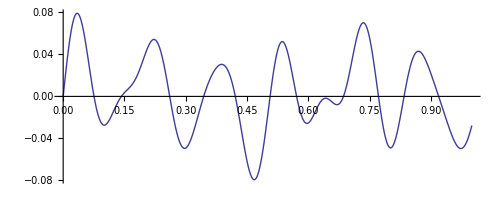

```mathematica
Plot[Evaluate[Sum[Sin[2 π RandomReal[{1,10}] x],{6}]/64],{x,0,1},AspectRatio->Automatic]
```

Here's the effect when it's applied to the brick wall.

```mathematica
BrickPlot[Evaluate[(1-(y/96))Sum[Sin[2 π RandomReal[{1,10}] x/192],{6}]], {x,0,192},{y,0,96},BrickSpacing->.5,StandardWallView[]]
```

-Graphics3D-

The variety of effects you can achieve is limited only by your inventiveness in creating surface functions, although if the displacement of the bricks is too large, the bricks will disengage and the wall will fall apart. More sophisticated methods of laying the bricks would permit greater displacement from the plane of the wall, but I wanted to keep things simple in this initial exploration.

Here are some examples of walls I explored. This wall uses the same idea as the previous one, but the straight part is at the midline rather than at the top.

```mathematica
BrickPlot[Evaluate[(1-(2y/96))Sum[Sin[2 π RandomReal[{1,10}] x/192],{6}]], {x,0,192},{y,0,96},BrickSpacing->.5,StandardWallView[]]
```

-Graphics3D-

This wall changes smoothly from one random sinusoid at the bottom to a different one at the top.

```mathematica
With[{
f1=Evaluate[Sum[ Sin[2 π RandomReal[{1,5}] x/96],{6}]],
f2=Evaluate[Sum[ Sin[2 π RandomReal[{1,5}] x/96],{6}]]
},
BrickPlot[f1 + (f2-f1)(y/96), {x,0,192},{y,0,96},StandardWallView[]]
]
```

-Graphics3D-

By randomizing the directions of the summed sinusoids as well as their frequencies, I generated walls with gently undulating, bumpy surfaces. In order to get a sense of the variety of this effect, I made a grid of random walls.

```mathematica
Grid[Table[BrickPlot[
Evaluate[Sum[Sin[2 π RandomReal[{-2,2},2].{x/64,y/64}],{7}]], {x,0,128},{y,0,64},BrickSpacing->4/3.,BrickStyle->{EdgeForm[None]},ImageSize->200,StandardWallView[]],{3},{2}],Spacings->0]
```

-Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D-

Somewhere along the course of this exploration, the phrase "the writing on the wall" popped into my head, and I wondered, could I do that? It turns out that it's incredibly easy with Mathematica.

It's so easy it's practically a one-liner, but I'll take it step-by-step so you can follow my thinking. It's a great demonstration of how having so much functionality in one integrated system makes it possible to explore with Mathematica where other programs can't go. My plan was to create a surface function that describes letters embossed in a surface, and feed that to BrickPlot.

First, I created an image by rasterizing some text.

```mathematica
textImage = Rasterize[Style["mirage",FontFamily->"Times"],ImageSize->196]
```

-Graphics-

Next, I blurred the image so that the edges of the letters in the surface would be rounded rather than abrupt steps. I converted that image from RGB to gray values and cropped to an aspect ratio of 1:2.

```mathematica
blurredTextImage = ImageCrop[ColorConvert[Blur[textImage],"GrayScale"],{256,128},Padding->1]
```

-Graphics-

This image contains discrete gray level values, but for BrickPlot, I needed a continuous function of x and y. I created that function using ListInterpolation after applying Transpose to the image data to account for a difference in the treatment of rows and columns between Image and Plot3D. I added some extra padding to the domain of the function because BrickPlot does some calculation outside of the nominal domain.

```mathematica
imageFunction=ListInterpolation[Transpose[ImageData[blurredTextImage]],{{0,256}+{-5,5},{0,128}+{-2.5,2.5}}];
```

```mathematica
Plot3D[ -3 imageFunction[x,y],{x,0,256},{y,0,128},BoxRatios->Automatic,PlotRange->All,MaxRecursion->4]
```

-Graphics3D-

Finally, I fed that surface function to BrickPlot, but I reduced the displacement of the bricks because I liked the idea of a subtle message that is revealed by the sun when it rakes across the wall at a shallow angle.

```mathematica
mirageWall=BrickPlot[ -imageFunction[x,y],{x,0,256},{y,0,128},BrickSpacing->1,BrickStyle->EdgeForm[None]]
```

-Graphics3D-

In order to explore the effect of the sun on the wall, I exported it as a DXF file and imported it into Google SketchUp.

```mathematica
Export["/Users/carlson/Documents/MirageWall.dxf",mirageWall]
```

/Users/carlson/Documents/MirageWall.dxf

Within SketchUp, I positioned the wall for maximum effect with respect to the path of the sun, and made this animation of the appearance of the wall in the course of a summer day.

-Graphics-

That's it. Five minutes from the conception of my writing-on-the-wall idea to an animation of its appearance. If only it were so easy to find a brick-laying robot.

## Implementation

```mathematica
SetOptions[$FrontEnd, RenderingOptions -> 
   {"HardwareAntialiasingQuality" -> 1}]
```

```mathematica
BrickPlot[functionExpr_, {xx_,xxMin_,xxMax_}, {yy_, yyMin_, yyMax_}, opts___]:=
Module[{bl, bw, bh, bs,nc,nb,bStyle,
surfaceFunction,slopeFunction},
{bl,bw,bh} = BrickSize /.{opts}/. {BrickSize->{8,4,2}};
bs = BrickSpacing/.{opts}/.{BrickSpacing->1};
bStyle = BrickStyle /. {opts}/.{BrickStyle->{}};
If[Head[bStyle]===List, bStyle=Directive@@bStyle];
nb= Floor[(xxMax-xxMin)/(bl + bs-.5)];
nc = Floor[(yyMax-yyMin)/bh];
surfaceFunction = Function[{xx,yy},functionExpr];
slopeFunction= Derivative[1,0][surfaceFunction];
Graphics3D[{0.8506752117189288,EdgeForm[{Black,Thickness[.0015]}],Antialiasing->True,bStyle,
Table[With[{
x=bl/2 + (b-1)(bl+bs) + If[EvenQ[c],0,(bl+bs)/2],
y=0,
z=c bh + bh/2
},Translate[Rotate[Cuboid[-{bl,bw,bh}/2.,{bl,bw,bh}/2.],-ArcTan[slopeFunction[x,z]],{0,0,1}],{x,y-surfaceFunction[x,z],z}]],{c,0,nc-1},{b,0,nb-1}]
},
Boxed->False,Lighting->"Neutral",Method->{"RotationControl"->"Globe"},
Select[{opts},((#[[1]]=!=BrickSize) && (#[[1]]=!=BrickSpacing)&& (#[[1]]=!=BrickStyle))&]
]
]
```

```mathematica
StandardWallView[]:= Sequence@@{
ViewPoint->{0.85,-1.45,0.17},ViewVertical->{0,0,1},
ImageSize->{400,229}};
```

```mathematica
HiRes[x_Graphics, n_:3]:=
Module[{size=ImageSize/.Options[x]},
If[!MatchQ[size,{_?NumericQ,_?NumericQ}],Return[$Failed]];
Show[Rasterize[Show[x,ImageSize->n size]],ImageSize->size]
]
```